# Exporter Test

### Generate Graph and Association from Twine Project

#### Importer

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=
	StringReplace[
		DeleteCases[
			StringCases[passageContent,{
				"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:> linkName,
				ShortestMatch["[["~~__~~ShortestMatch["->"~~linkName__]~~"]]"] :> linkName,
				ShortestMatch["[["~~__~~ShortestMatch["|"~~linkName__]~~"]]"] :> linkName,
				ShortestMatch["[["~~ShortestMatch[linkName__ ~~ "<-"]~~__~~"]]"] :> linkName
				}],
		{}], {"&quot;" -> "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'", "&amp;" -> "&", "&nbsp;" -> WhitespaceCharacter}]
```

```mathematica
Clear[twineImport]
twineImport[absoluteFilePath_String]:= Module[{fileAsString,fileSansHeader,file,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,psgAssocCleaned,assocForm,edges,alledges, g, v},
	fileAsString = Import[absoluteFilePath, "String"];
	fileSansHeader = StringCases[fileAsString, htmlHeader___~~ important:("<tw-storydata"~~ ___ ~~ "</tw-storydata>")~~___ ~~EndOfString:> important](*/.{fileString_}->fileString*);
	file = If[ListQ[fileSansHeader], fileSansHeader /.{fileString_} -> fileString, fileSansHeader ];
	testString = file;
	xmlObject = parseXML[file];

	rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
	rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
	passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];

	passageContentThread= 
		AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧,
			{
				"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:>linkName,
				ShortestMatch["[["~~hiddenName__~~ShortestMatch["->"~~__]~~"]]"] :> hiddenName,
				ShortestMatch["[["~~hiddenName__~~ShortestMatch["|"~~__]~~"]]"] :> hiddenName,
				ShortestMatch["[["~~ShortestMatch[__ ~~ "<-"]~~hiddenName__~~"]]"] :> hiddenName
			}]];
	
	passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
	
	edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
	alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
	g =Graph[alledges];
	v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
	completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}];

	assocForm = Block[{passageContentWithLinks,completeAssociation},
		(*Create Assocation between passage and content for tooltips and remove the link syntax*)
		passageContentWithLinks= AssociationThread[Transpose[passages]⟦1⟧ -> Transpose[passages]⟦2⟧];
		(*Root Node Association*)
		completeAssociation = <|rootNodeName -> passageContentWithLinks|>];
		(*Echo[assocForm, "ASSOC FORM "];*)
{completeGraph, assocForm}
]
twineImport::usage = "twineImport[path/to/file.html] gives a graph and an association of a Twine 2 project";
```

#### Exporter : Rewrite

```mathematica
Clear[twineExport]
twineExport[associationForm_Association, exportPathToFile_]:=Module[{storyAssoc = associationForm,twGraphVertices,twGraphPoints,sTemplateHeader,assocLength,passageAssoc,passages, stringOfStory},
(*Grab Vertex Points for Passage Positions*)
twGraphVertices = GraphEmbedding[twineSummary[storyAssoc, "Graph"]];
Echo[twGraphVertices, "Graph Vertices "];
twGraphPoints = Reverse[Rescale[Rescale[twGraphVertices],{-1,1}, {0, 250}]];
Echo[twGraphPoints, "Graph Points for Twine "];
sTemplateHeader = StringTemplate["
<tw-storydata name=\"`storyTitle`\" startnode=\"1\" creator=\"Twine\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>

  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">
  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">
  </script>
"
][<|"storyTitle" -> First[Keys[storyAssoc]]|>];
passageAssoc = First[Values[storyAssoc]];
assocLength = Length[passageAssoc];
passages = Table[
StringTemplate["<tw-passagedata pid=\"`pid`\" 
name=\"`passagename`\" 
tags=\"\"
position=\"`xPos`,`yPos`\"
size=\"100,100\"
>`content`</tw-passagedata>"][<|"pid"-> index,"passagename" -> Keys[passageAssoc]⟦index⟧, "content" -> Values[passageAssoc]⟦index⟧, "xPos" -> twGraphPoints⟦index⟧⟦1⟧, "yPos" -> twGraphPoints⟦index⟧⟦2⟧ |>], {index, 1,assocLength,1}];
stringOfStory= StringJoin[{sTemplateHeader, passages, "</tw-storydata>"}];
Export[exportPathToFile <>".html",stringOfStory , "HTMLFragment"]
]
twineExport::usage = "twineExport[<| key1 → val1 ... |>, path/to/file] Exports WL Twine Representation to the specified path";
```

```mathematica
twineAssoc
```

<|TwineBridge_Test→<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>|>

```mathematica
twineAssoc["TwineBridge_Test"]["First Passage"]
```

This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?

```mathematica
Values[twineAssoc]//First
```

<|First Passage→This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?,Left→From here, there are still other places to go. We can go [[Up]] or [[Down]],Right→From here, there are still other places to go. We can go [[Up]] or [[Down]],Up→Now that we are up why don&#39;t we [[get going]]?,Down→Now that we are down, why don&#39;t we get [[Up]]?,get going→Now that we are going, how about we [[do something]],do something→ Hi, I&#39;m doing something, why don&#39;t [[you do something]]?,you do something→ Go, Get out of here! |>

```mathematica
twineExport[twineAssoc, "~/Desktop/newForm-export-01"]
```

~/Desktop/newForm-export-01.html

#### Summarizer (Graph, Graph + Passage Display, Export)

```mathematica
Clear[cleanPassages]
cleanPassages[passageAssoc_]:= Module[{markdownReplacements,psgContent,psgContentNoLinks,psgContentMarkdownReplaced }, 
	markdownReplacements = {"&quot;" -> "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'"};
	psgContent = Table[generateEdges[Flatten[Keys[Values[passageAssoc]]]⟦index⟧,Flatten[Values[Values[passageAssoc]]]⟦index⟧], {index, 1, Length[Values[passageAssoc]/.{assc_}:> assc],1}];
	psgContentNoLinks = (psgContent /. DirectedEdge[id_,content_]:> DirectedEdge[id, StringReplace[content, 
	{"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:>linkName,
		ShortestMatch["[["~~hiddenName__~~ShortestMatch["->"~~__]~~"]]"] :> hiddenName,
		ShortestMatch["[["~~hiddenName__~~ShortestMatch["|"~~__]~~"]]"] :> hiddenName,
		ShortestMatch["[["~~ShortestMatch[__ ~~ "<-"]~~hiddenName__~~"]]"] :> hiddenName,
		"&quot;" -> "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'", "&nbsp;" -> " ","&amp;" -> "&"
		}
	
	]]);
	psgContentMarkdownReplaced = (psgContentNoLinks /. DirectedEdge[id_,content_]:> DirectedEdge[id, StringReplace[content, markdownReplacements]])
]
```

```mathematica
Clear[twineSummary]
twineSummary[userAssoc_, outputForm_:"Summary"]:= Module[{firstEdge, passageEdges,cleanedPassages,buttonList,buttonGraph},

	Module[{activePassage = First[Keys[userAssoc]], psgKeys = Flatten[Keys[Values[userAssoc]]]},

	(*First Edge*)
	firstEdge = {First[Keys[userAssoc]]-> Flatten[Keys[Values[userAssoc]]]⟦1⟧};

	(*Passage Edges*)
	passageEdges = Flatten@DeleteCases[Table[generateEdges[psgKeys⟦index⟧, extractLinks[Flatten[Values[Values[userAssoc]]]⟦index⟧]], {index, 1, Length[Values[userAssoc]/.{assc_}:> assc],1}], {}];

	(*Passage Content Clean*)
	cleanedPassages = cleanPassages[userAssoc];

	(*List of Buttons*)
	buttonList = cleanedPassages/. DirectedEdge[name_, content_] :> Button[name, activePassage = content];

	(*Replace the vertices of the graph with the buttons*)
	buttonGraph = 
		VertexReplace[
			Graph[Flatten[firstEdge~Join~passageEdges],
			VertexShapeFunction->"Name",
			GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->First[Keys[userAssoc]]}], Table[psgKeys⟦i⟧ -> buttonList⟦i⟧, {i, Length[psgKeys]}]];
(*
	Summary ⇒ {Edges, Simple Graph} 
	Graph   ⇒ Simple Graph
	Export  ⇒ Exports Story to TwineStories folder in current directory
*)

	Switch[outputForm,
		"Summary", GraphicsRow[{Dynamic[Framed[activePassage]] , buttonGraph}],
		"Graph", buttonGraph,
		"Export",
			If[DirectoryQ[FileNameJoin[{NotebookDirectory[], "TwineStories"}]],
				Block[{twineFolder},
					twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
					twineExport[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
				],
				Block[{twineFolder},
					twineFolder = FileNameJoin[{NotebookDirectory[], "TwineStories"}];
					CreateDirectory[twineFolder];
					twineExport[userAssoc, twineFolder <> "/"<> ToString[First[Keys[userAssoc]]]]
				]
			];
		]
]]
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>, \"Export\"] Exports WL Twine Representation to the TwineStories folder in the Current Notebook Directory";
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>, \"Graph\"] Generates Twine Graph";
twineSummary::usage = "twineSummary[<| key1 → val1 ... |>] Displays the Twine Passages and the Graph";
```

```mathematica
Association@@{"this" -> "that", "other" -> "thing"}
```

<|this→that,other→thing|>

### Import Twine Story

```mathematica
Clear[twineGraph, twineAssoc]
{twineGraph, twineAssoc} =twineImport["~/Documents/Twine/Stories/TwineBridge_Test.html"];
```

```mathematica
testingAssoc
```

<|Other Story→<|Two→Go to passage [[Three]],Three→Here we are at Passage Three|>|>

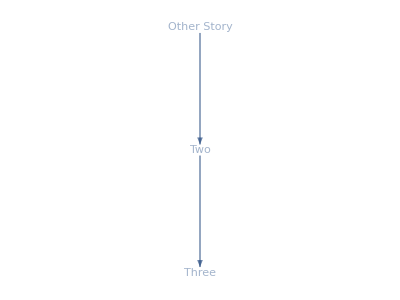

```mathematica
twineSummary[testingAssoc]
```

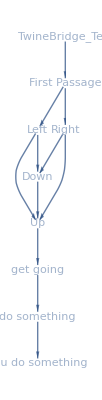

```mathematica
twineSummary[twineAssoc]
```

### Different Forms

```mathematica
testingAssoc =<|"Other Story" -><|"Two" -> "Go to passage [[Three]]", "Three" ->  "Here we are at Passage Three"|>|>;
```

```mathematica
twineSummary[testingAssoc]
```

-Graphics-

```mathematica
twineAssocNewForm = <|"TwineBridge_Test"-><|"First Passage"->"This is my first passage. Where can I go from here? How about [[Left]] , or [[Right]]?","Left"->"From here, there are still other places to go. We can go [[Up]] or [[Down]]","Right"->"From here, there are still other places to go. We can go [[Up]] or [[Down]]","Up"->"Now that we are up why don&#39;t we [[get going]]?","Down"->"Now that we are down, why don&#39;t we get [[Up]]?","get going"->"Now that we are going, how about we [[do something]]","do something"->" Hi, I&#39;m doing something, why don&#39;t [[you do something]]?","you do something"->" Go, Get out of here! "|>|>;
```

```mathematica
twineSummary[twineAssocNewForm]
```

-Graphics-

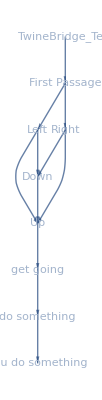

```mathematica
twineSummary[twineAssocNewForm, "Graph"]
```

```mathematica
twineSummary[twineAssocNewForm, "Export"]
```

Graph Vertices  {{0.,7.},{0.,6.},{-1.,5.},{0.,5.},{-1.,3.},{-1.,4.},{-1.,2.},{-1.,1.},{-1.,0.}}

Graph Points for Twine  {{0.,250.},{0.,500.},{0.,750.},{0.,1250.},{0.,1000.},{250.,1500.},{0.,1500.},{250.,1750.},{250.,2000.}}

The issue now: Need to LOCALIZE the Dynamic Variable, so for each story that is Summarized in a notebook the passages won’t interfere.

```mathematica
twineSummary[twineAssocNewForm, "Export"]
```

### Position of Passages

I can use the vertex positions from the graph for passage positions 
Let’s work on extracting those things.

```mathematica
Graph[{1,2, 3}, {1->2, 2->3,3 -> 1}]//GraphEmbedding
```

{{-0.866025,-0.5},{0.866025,-0.5},{1.83697×10^-16,1.}}

```mathematica
Rescale[%2562 , {Min[%2562], Max[%2562]}, {0, 100}]
```

{{0.,19.6152},{92.8203,19.6152},{46.4102,100.}}

```mathematica
GraphicsRow[{Column@GraphEmbedding@twineSummary[twineAssocNewForm, "Graph"],twineSummary[twineAssocNewForm, "Graph"] }]
```

-Graphics-

```mathematica
Rescale[Rescale[%2573 ],{0,1}, {0,500}]
```

{{62.5,500.},{62.5,437.5},{0.,375.},{62.5,375.},{0.,250.},{0.,312.5},{0.,187.5},{0.,125.},{0.,62.5}}

```mathematica
Reverse/@%2619
```

{{500.,62.5},{437.5,62.5},{375.,0.},{375.,62.5},{250.,0.},{312.5,0.},{187.5,0.},{125.,0.},{62.5,0.}}

```mathematica
{{-1, 0}, {0, 0}, {1, 0}}
```

```mathematica
Transpose[{{-1, 0}, {0, 0}, {1, 0}}]
```

{{-1,0,1},{0,0,0}}

```mathematica
Rescale[#]&/@%2712
```

{{0,1/2,1},{0,0,0}}

```mathematica
Rescale[%2713, {0,1}, {10, 390}]
```

{{10,200,390},{10,10,10}}

```mathematica
Rescale[{{-1, 0}, {0, 0}, {1, 0}}, {-1, 1}, {10, 390}]
```

{{10,200},{200,200},{390,200}}

### Larger Stories

First : Strip out HTML header stuff and leave just the <tw-storydata> and <tw-passagedata>

```mathematica
Clear[twLargeGraph,twLargeAssoc]
{twLargeGraph, twLargeAssoc} =twineImport["~/Desktop/DepthsOfSarcasmV17.html"];
```

```mathematica
twineSummary[twLargeAssoc]
```

-Graphics-

```mathematica
{twISCGraph,twISCAssoc}=twineImport["~/Documents/Twine/Stories/isc405 _ Assignment 3.html"];
```

```mathematica
twineSummary[twISCAssoc]
```

-Graphics-

```mathematica
twineSummary[twISCAssoc, "Export"]
```

Graph Vertices  {{0.,7.},{0.,3.},{1.,2.},{1.,5.},{1.,4.},{0.,1.},{1.,1.},{2.,1.},{1.,3.},{-2.,7.},{-2.,6.},{-1.,7.},{-2.,5.},{-2.,4.},{-1.,4.},{-1.,0.},{0.,0.},{1.,0.},{2.,0.}}

Graph Points for Twine  {{180.556,152.778},{166.667,152.778},{152.778,152.778},{138.889,152.778},{138.889,208.333},{125.,208.333},{125.,222.222},{138.889,250.},{125.,236.111},{125.,250.},{166.667,194.444},{180.556,166.667},{166.667,166.667},{152.778,166.667},{166.667,208.333},{166.667,222.222},{166.667,180.556},{152.778,194.444},{152.778,250.}}

#### Removing HTML Header

```mathematica
fString = Import["~/Desktop/DepthsOfSarcasmV17.html", "String"];
```

```mathematica
StringTake[fString, 23]
```

<!DOCTYPE html>
<html>

```mathematica
StringCases[fString, htmlHeader___~~ important:("<tw-storydata"~~ ___ ~~ "</tw-storydata>")~~___ ~~EndOfString:> important]
```

{<tw-storydata name="DepthsOfSarcasmV17" startnode="1" creator="Twine" creator-version="2.0.10" ifid="9ACF5B91-2190-43BC-A1EE-1B9FA0898772" format="Harlowe" options="" hidden><style role="stylesheet" id="twine-user-stylesheet" type="text/twine-css">tw-sidebar {
    display: none;
}




























</style><script role="script" id="twine-user-script" type="text/twine-javascript">




























</script><tw-passagedata pid="1" name="start" tags="" position="1302,115">(text-style: &quot;superscript&quot;)[(align: &quot;==&gt;&quot;)[(c) 2016 Sam Wilson
Version 1.7.3] ]

(display: &quot;startup&quot;)(set: $goldtogo to 1000-$gold)Journey into...

(text-style: &quot;bold&quot;)[THE DEPTHS OF SARCASM]

(either: &quot;Great title.&quot;,&quot;A legitimate way to spend your time.&quot;,&quot;A thrilling adventure.&quot;)

You&#39;re on a quest to collect 1000 gold pieces because you&#39;re really imaginative.

The entrance of a cave in front of you.

[[Enter the cave-&gt;newroom]]









</tw-passagedata>
<tw-passagedata pid="2" name="newroom" tags="" position="2011,112">You enter a (either: &quot;dingy&quot;, &quot;dank&quot;, &quot;miserable&quot;, &quot;poorly-lit&quot;, &quot;gross&quot;,&quot;slimy&quot;,&quot;gloomy&quot;,&quot;depressing&quot;,&quot;musty-smelling&quot;,&quot;fetid&quot;,&quot;reeking&quot;) (either: &quot;chamber&quot;, &quot;cavern&quot;, &quot;room&quot;, &quot;tunnel&quot;, &quot;nook&quot;, &quot;vault&quot;,&quot;crypt&quot;,&quot;passage&quot;).

(set: $coinflip to (random: 1, 5))(if: $coinflip is 1)[(either:&quot;A monster leaps out at you.&quot;,&quot;A monster drops down on you.&quot;,&quot;A monster crawls out of the shadows.&quot;,&quot;You walk straight into a monster.&quot;,&quot;Oh look. A monster. What a surprise.&quot;,&quot;And is that a monster over there? Of course it is.&quot;)

[[Fight the monster-&gt;newmonster]] ](if: $coinflip is 2)[You find a treasure chest. (either: &quot;Because everyone leaves treasure chests lying around.&quot;, &quot;Like you do.&quot;, &quot;Great.&quot;)

[[Open the chest-&gt;chest]]
[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ](if: $coinflip&gt;2)[(either: &quot;This place is brimming with excitement.&quot;, &quot;This place is just the best.&quot;, &quot;You can&#39;t get over how awesome it is.&quot;, &quot;Fantastic.&quot;, &quot;Just wow.&quot;,&quot;Lovely.&quot;,&quot;Epic.&quot;,&quot;You seriously consider settling down here and picking out curtains.&quot;)

[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ]
(if: $coinflip&gt;1 and $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ]

</tw-passagedata>
<tw-passagedata pid="3" name="drink a potion" tags="" position="2143,1059">(set: $potions to $potions-1)(if: $hp is $maxhp)[(either:&quot;You were already at full health, genius.&quot;,&quot;Yeah. You really needed to do that.&quot;,&quot;Oh boy, what a great use of a potion.&quot;,&quot;Some people would consider that a spectacular waste.&quot;,&quot;Drinking a potion when you&#39;re already at full health? Well done.&quot;)

](if: $hp &lt; $maxhp)[(set: $hp to it+10)You are healed by 10 hit points.

](if: $hp&gt;$maxhp)[(set: $hp to $maxhp)You&#39;re at maximum health. 

](if: $potions&gt;0)[ [[Drink another potion-&gt;drink a potion]] 
][[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="4" name="hit" tags="" position="1407,1466">(set: $attackpower to (random: $xp,$xp*5)+$sword)(set: $monsterhealth to it-$attackpower)(if: $monsterhealth&lt;1)[(set: $monsterhealth to 0)](either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;) You hit the $monstername for $attackpower damage.

The $monstername&#39;s health is $monsterhealth.

(if: $monsterhealth&gt;0)[It attacks.

[[Defend-&gt;defend]]
[[Run away-&gt;runaway]] 
](if: $bribeammount&lt;$gold and $hp&gt;0 and $monsterhealth&gt;0)[ [[Bribe-&gt;bribe]] 
](if: $monsterhealth&lt;1)[You won. (either: &quot;Woo.&quot;,&quot;Whoopee.&quot;,&quot;Go you.&quot;,&quot;What a champ.&quot;,&quot;Staggering.&quot;,&quot;Inspiring.&quot;,&quot;You&#39;re amazing.&quot;,&quot;You probably deserve a parade.&quot;,&quot;We&#39;re all so proud.&quot;)

[[Loot the room-&gt;win]] ]

</tw-passagedata>
<tw-passagedata pid="5" name="bribe" tags="" position="1069,1630">(set: $gold to $gold-$bribeammount)The $monstername takes $bribeammount gold coins from you and kicks you out the door. Because (print: $monstername+&quot;s&quot;) need gold, I guess. Yeah, authentic.

[[Continue exploring-&gt;newroom]] </tw-passagedata>
<tw-passagedata pid="6" name="runaway" tags="" position="1076,1445">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $hp to $hp-$damage)(either: &quot;Truely you are the hero that the world needs.&quot;,&quot;So inspiring.&quot;,&quot;A picture of bravery.&quot;,&quot;Lion-hearted. Really.&quot;,&quot;Gallant.&quot;)

As you run away the $monstername hits you for $damage damage.

(if: $hp &gt; 0)[ [[Continue exploring-&gt;newroom]] ]
(if: $potions&gt;0 and $hp &gt; 0)[ [[Drink a potion-&gt;drink a potion]] ]
(if: $hp &lt; 1)[ You are so dead.  

[[Game over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="7" name="newmonster" tags="" position="1507,1288">(set: $monsterid to (random: 1,10))(set: $monstername to $monsterid of $monsterarray)(set: $monsterlevel to (random: $xp, $xp+2))(set: $imonsterhealth to $monsterlevel*3)(set: $monsterhealth to $imonsterhealth+7)(set: $bribeammount to $monsterlevel*10)You are fighing a level $monsterlevel $monstername. (either: &quot;What an ugly bastard.&quot;,&quot;It&#39;s quite the looker.&quot;,&quot;You can tell you&#39;re going to be besties.&quot;,&quot;Sigh.&quot;,&quot;Let&#39;s get this over with.&quot;,&quot;Oh joy.&quot;) It has $monsterhealth health.

 [[Hit the monster-&gt;hit]]
 [[Run away-&gt;runaway]]
 (if: $bribeammount&lt;$gold)[ [[Bribe the monster-&gt;bribe]] 
](if: $potions&gt;0)[ [[Drink a potion-&gt;battledrink]] 
](if: $poisons&gt;0)[ [[Throw a poison-&gt;battlepoison]] 
]</tw-passagedata>
<tw-passagedata pid="8" name="defend" tags="" position="1418,1625">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $damage to $damage-$shield)(if: $damage&lt;0)[(set: $damage to 0)](set: $hp to $hp-$damage)(either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;) The $monstername hits you for $damage damage.

(if: $hp&lt;1)[ You are so dead.

[[Game over-&gt;gameover]] ](if: $hp&gt;0)[The $monstername has $monsterhealth health. 

](if: $hp&gt;0)[ [[Hit it again-&gt;hit]]
[[Run away-&gt;runaway]]
](if: $bribeammount&lt;$gold and $hp&gt;0)[ [[bribe]] 
](if: $potions&gt;0 and $hp&gt;0)[ [[Drink a potion-&gt;battledrink]] 
](if: $poisons&gt;0 and $hp&gt;0)[ [[Throw a poison-&gt;battlepoison]] 
]</tw-passagedata>
<tw-passagedata pid="9" name="win" tags="" position="1075,1281">You go up a level. (either: &quot;Because levels are real things.&quot;,&quot;Don&#39;t break anything with your amazing new powers.&quot;,&quot;Hail the conquering hero.&quot;,&quot;So, yay, progress.&quot;,&quot;It looks like you needed it.&quot;)

(set: $cashammount to (random: $monsterlevel, $monsterlevel*10))(set: $gold to $gold+$cashammount)(set: $xp to $xp+1)(set: $monsterkills to it+1)(either:&quot;You found $cashammount gold coins in the dead $monstername&#39;s pockets.

A $monstername with pockets. Yeah.&quot;,&quot;You pick up $cashammount gold coins that are scattered across the floor.&quot;,&quot;You drag the $monstername&#39;s corpse to the village taxidermist and collect a bounty of $cashammount gold coins.&quot;,&quot;You find $cashammount gold coins on one of the corpses scattered around the room.&quot;,&quot;You cut the $monstername&#39;s body open and $cashammount gold coins fall out. What a believable thing to happen.&quot;)
(if: $gold&lt;1000)[
[[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]]
(if: $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ] ](if: $gold&gt;999)[
You know what that means? You just won the game.

[[Game Over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="10" name="battledrink" tags="" position="1578,1459">(set: $potions to $potions-1)You are healed by 10 hit points. (if: $hp is $maxhp)[But you were already at maximum health. So that was a potion well-spent. Just so we&#39;re on the same page here:](set: $hp to it+10)(if: $hp&gt;=$maxhp)[(set: $hp to $maxhp)

You&#39;re at maximum health.]

(if: $potions &gt; 0)[[[Drink another-&gt;battledrink]]
][[Fight-&gt;defend]]</tw-passagedata>
<tw-passagedata pid="11" name="market" tags="" position="3530,300">(if: $visitedmarket is false)[You head out of the caves and back to the local village, which is a bustling metropolis called &quot;Pigswill&quot;. The storekeeper greets you with a belch.(set: $visitedmarket to true)

]You look at the wares on sale.(if: $gold&lt;10)[

There&#39;s nothing you can afford.]

(if: $potions&gt;0)[ [[Sell a potion for 5 gold-&gt;sell potion]] 
](if: $poisons&gt;0)[ [[Sell a poison for 10 gold-&gt;sell poison]] 
](if: $gold&gt;24)[ [[Buy a cardboard shield for 25 gold-&gt;buy shield]] 
](if: $gold&gt;49)[ [[Buy a wooden sword for 50 gold-&gt;buy sword]]
](if: $gold&gt;74)[ [[Buy a wooden shield for 75 gold-&gt;buy shield2]] 
](if: $gold&gt;99)[ [[Buy a tin sword for 100 gold-&gt;buy sword2]]
](if: $gold&gt;9)[ [[Buy a potion for 10 gold-&gt;buy potion]] 
](if: $gold&gt;19)[ [[Buy a poison for 20 gold-&gt;buy poison]] 
][[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="12" name="buy potion" tags="" position="3327,512">(set: $gold to it-10)(set: $potions to it+1)Magic potion. A totally real thing. 

[[Continue shopping-&gt;market]]
[[Drink the potion-&gt;drink a potion]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="13" name="buy shield" tags="" position="3550,617">(set: $gold to it-25)(if: $shield is 0)[You pick up your new cardboard shield. You&#39;re safe now. This game is as good as won.](if: $shield is 5)[Yeah, you can never waste enough gold coins on identical cardboard shields.](if: $shield is 10)[You had a wooden shield that was capable of protecting you against double the damage, but no, whatever you want. You toss your significantly better shield aside and take your new cardboard shield.](set: $shield to 5)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="14" name="buy sword" tags="" position="3259,137">(set: $gold to it-50)(if: $sword is 0)[Wood. The substance with amazing slicing properties. Hence the well known expression &quot;As sharp as wood.&quot;](if: $sword is 10)[You already have one of those, but fine. You throw it away and take this one. Because clearly the old one wasn&#39;t exactly as good in every way. This new one is one beautiful wooden sword.](if: $sword is 20)[You... you had a better sword. You just threw it away for this sword. Made of wood. 

Masterful. We&#39;re in awe.]


(set: $sword to 10)[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="15" name="sell potion" tags="" position="3732,117">(set: $gold to it+5)(set: $potions to it-1)(if: $gold&lt;1000)[Five gold? (either: &quot;What a rip-off.&quot;,&quot;You&#39;re a real entrepreneur.&quot;)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]]
(if: $gold&gt;999)[So you just won the game. By selling a potion. What a climax.

[[Game Over-&gt;gameover]] ]

</tw-passagedata>
<tw-passagedata pid="16" name="Footer" tags="footer" position="22,300">



   (set: $ihp to $xp*3)(set: $maxhp to $ihp+7)Health: $hp/$maxhp Gold: $gold Potions: $potions Poisons: $poisons 
   Experience Level: $xp
   Shield: (if: $shield is 0)[None.](if: $shield is 5)[Cardboard.](if: $shield is 10)[Wood.] Sword: (if: $sword is 0)[A stick.](if: $sword is 10)[Wood.](if: $sword is 20)[Tin.]
   ] ] ]</tw-passagedata>
<tw-passagedata pid="17" name="startup" tags="startup" position="20,3">(set: $first to true)(set: $visitedmarket to false)(set: $shield to 0)(set: $sword to 0)(set: $hp to 10)(set: $gold to 0)(set: $xp to 1)(set: $potions to 3)(set: $poisons to 0)(set: $monsterarray to (a: &quot;cave eel&quot;,&quot;toadwolf&quot;,&quot;octopus&quot;,&quot;lurking shadow&quot;,&quot;fang vortex&quot;,&quot;battlecrab&quot;,&quot;maw&quot;,&quot;Thing From Beyond&quot;, &quot;slither&quot;,&quot;lunk ape&quot;))(set: $monsterkills to 0)</tw-passagedata>
<tw-passagedata pid="18" name="header" tags="header" position="26,147">(background: black)[(colour: green)[(font: &#39;courier&#39;)[ </tw-passagedata>
<tw-passagedata pid="19" name="chest" tags="" position="2705,1261">(set: $coinflip to (random: 1,4))(either:&quot;You pry open the chest with your (if:$sword is 0)[stick.](if:$sword is 10)[wooden sword.](if:$sword is 20)[tin sword.]&quot;,&quot;You open the chest with one of the keys lying around. Yeah, any key can open any chest around here. That&#39;s just basic security.&quot;)

(if: $coinflip is 1)[A monster leaps out. (either: &quot;It was hiding in there. Curled up real small.&quot;,&quot;It&#39;s been hiding in there for a while. It&#39;s obviously a busy creature with a lot going on in its life.&quot;,&quot;Boo.&quot;,&quot;And you thought the day couldn&#39;t get better.&quot;)

[[Fight the monster-&gt;newmonster]] ](if: $coinflip &gt; 1)[(set: $newgold to (random: $xp, $maxhp))(set: $gold to it+$newgold)(if: $gold&lt;1000)[You find $newgold gold coins. (either:&quot;What a bounty.&quot;,&quot;Whoop dee doo.&quot;,&quot;Go you.&quot;)] ]

(if: $coinflip &gt; 2 and $gold&lt;1000)[(set: $potions to it+1) And you also find a potion. (either:&quot;So there&#39;s that.&quot;,&quot;Yay.&quot;,&quot;Hurrah.&quot;)

](if: $coinflip &gt; 3 and $gold&lt;1000)[(set: $poisons to it+1) And a poison. (either:&quot;Look at you go.&quot;,&quot;You&#39;re on such a roll.&quot;)

](if: $coinflip&gt;1 and $gold&lt;1000)[ [[Continue exploring-&gt;newroom]]
[[Go to the market-&gt;market]] ](if: $gold&gt;999)[You have more than a thousand gold coins. So you&#39;ve won.

[[Game Over-&gt;gameover]] ]
(if: $coinflip&gt;1 and $potions&gt;0 and $gold&gt;999)[ [[Drink a potion-&gt;drink a potion]] ]</tw-passagedata>
<tw-passagedata pid="20" name="buy shield2" tags="" position="3730,508">(set: $gold to it-75)(if: $shield &lt; 10)[A wooden shield. You&#39;re now completely and totally invulnerable, assuming that you don&#39;t encounter fire, acid, arrows, swords, fast-moving rocks, clubs, maces, magic bolts, rays of frost, enemies of any kind, or woodworms.](if: $shield is 10)[You can never have enough of these. Apparently.](set: $shield to 10)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="21" name="buy sword2" tags="" position="3521,64">(set: $gold to it-100)(if: $sword &lt; 20)[Tin. A tin sword. Worth every one of the hundred coins of actual gold that you&#39;ve just given away for it.](if: $sword is 20)[Another identical tin sword. No, you go ahead, buy it. You evidently know what you&#39;re doing.](set: $sword to 20)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="22" name="buy poison" tags="" position="3245,307">(set: $gold to it-20)(set: $poisons to it+1)(if: $poisons is 1)[A deadly liquid that looks almost identical to all the other potions that you&#39;re drinking. This will end well.

]You take a bottle of poison.

[[Continue shopping-&gt;market]]
[[Drink the potion-&gt;drink a potion]]
[[Continue exploring-&gt;newroom]]</tw-passagedata>
<tw-passagedata pid="23" name="sell poison" tags="" position="3766,300">(set: $gold to it+10)(set: $poisons to it-1)(if: $gold&lt;1000)[(either: &quot;You sell it for half the price you normally buy it for. Way to go.&quot;,&quot;Yeah, that probably wouldn&#39;t have been useful in that in EVERY SINGLE BATTLE.&quot;)

[[Continue shopping-&gt;market]]
[[Continue exploring-&gt;newroom]] ](if: $gold&gt;999)[You just won the game by selling a poison.

What a satisfying ending.

[[Game Over-&gt;gameover]] ]</tw-passagedata>
<tw-passagedata pid="24" name="battlepoison" tags="" position="1587,1631">Poison. The heroic way to win a fight. You throw a bottle at the $monstername.

(set: $coinflip to (random:1,2))(if: $coinflip is 1)[It misses.

[[Nice aim, jackass-&gt;hit]] ](if: $coinflip is 2)[(set: $monsterhealth to it-10)It goes into its mouth.

The monster is distracted. And poisoned. Obviously.

[[Hit the monster-&gt;hit]] ]</tw-passagedata>
<tw-passagedata pid="25" name="gameover" tags="" position="1307,380">(text-style: &quot;bold&quot;)[THANK YOU FOR PLAYING THE DEPTHS OF SARCASM
(either:&quot;HAVE A WONDERFUL DAY&quot;,&quot;WHAT AN AMAZING PERFORMANCE&quot;,&quot;YOU MUST BE SO PROUD&quot;,&quot;GREAT JOB ALL ROUND&quot;,&quot;DON&#39;T FORGET TO TIP THE MONSTERS&quot;,&quot;CLOSE THE DOOR ON YOUR WAY OUT&quot;,&quot;YOU WERE AN AMAZING PLAYER&quot;)]

You collected $gold gold coins and defeated $monsterkills monsters.

[[Play again-&gt;start]]</tw-passagedata>
</tw-storydata>}

### Replacing Markdown syntax with sensible text

A macro command in Twine is defined by:  ( <command> : <directive>)

A variable in Twine is defined by: $<variable-name>

Setting a variable: (set : <variable>  to <expression>)

```mathematica
testString =""
```

```mathematica
testString
```

<tw-storydata name="DepthsOfSarcasmV17" startnode="1" creator="Twine" creator-version="2.0.10" ifid="9ACF5B91-2190-43BC-A1EE-1B9FA0898772" format="Harlowe" options="" hidden>
    <style role="stylesheet" id="twine-user-stylesheet" type="text/twine-css">tw-sidebar { display: none; }










    </style>
    <script role="script" id="twine-user-script" type="text/twine-javascript">










    </script>
    <tw-passagedata pid="1" name="start" tags="" position="1302,115">(text-style: &quot;superscript&quot;)[(align: &quot;==&gt;&quot;)[(c) 2016 Sam Wilson Version 1.7.3] ] (display: &quot;startup&quot;)(set: $goldtogo to 1000-$gold)Journey into... (text-style: &quot;bold&quot;)[THE DEPTHS OF SARCASM] (either: &quot;Great
      title.&quot;,&quot;A legitimate way to spend your time.&quot;,&quot;A thrilling adventure.&quot;) You&#39;re on a quest to collect 1000 gold pieces because you&#39;re really imaginative. The entrance of a cave in front of you. [[Enter the cave-&gt;newroom]]









    </tw-passagedata>
    <tw-passagedata pid="2" name="newroom" tags="" position="2011,112">You enter a (either: &quot;dingy&quot;, &quot;dank&quot;, &quot;miserable&quot;, &quot;poorly-lit&quot;, &quot;gross&quot;,&quot;slimy&quot;,&quot;gloomy&quot;,&quot;depressing&quot;,&quot;musty-smelling&quot;,&quot;fetid&quot;,&quot;reeking&quot;)
      (either: &quot;chamber&quot;, &quot;cavern&quot;, &quot;room&quot;, &quot;tunnel&quot;, &quot;nook&quot;, &quot;vault&quot;,&quot;crypt&quot;,&quot;passage&quot;). (set: $coinflip to (random: 1, 5))(if: $coinflip is 1)[(either:&quot;A monster leaps
      out at you.&quot;,&quot;A monster drops down on you.&quot;,&quot;A monster crawls out of the shadows.&quot;,&quot;You walk straight into a monster.&quot;,&quot;Oh look. A monster. What a surprise.&quot;,&quot;And is that a monster over there? Of
      course it is.&quot;) [[Fight the monster-&gt;newmonster]] ](if: $coinflip is 2)[You find a treasure chest. (either: &quot;Because everyone leaves treasure chests lying around.&quot;, &quot;Like you do.&quot;, &quot;Great.&quot;) [[Open the chest-&gt;chest]]
      [[Continue exploring-&gt;newroom]] [[Go to the market-&gt;market]] ](if: $coinflip&gt;2)[(either: &quot;This place is brimming with excitement.&quot;, &quot;This place is just the best.&quot;, &quot;You can&#39;t get over how awesome it is.&quot;,
      &quot;Fantastic.&quot;, &quot;Just wow.&quot;,&quot;Lovely.&quot;,&quot;Epic.&quot;,&quot;You seriously consider settling down here and picking out curtains.&quot;) [[Continue exploring-&gt;newroom]] [[Go to the market-&gt;market]] ] (if: $coinflip&gt;1
      and $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ]

    </tw-passagedata>
    <tw-passagedata pid="3" name="drink a potion" tags="" position="2143,1059">(set: $potions to $potions-1)(if: $hp is $maxhp)[(either:&quot;You were already at full health, genius.&quot;,&quot;Yeah. You really needed to do that.&quot;,&quot;Oh boy, what a great use of a potion.&quot;,&quot;Some people would consider that a
      spectacular waste.&quot;,&quot;Drinking a potion when you&#39;re already at full health? Well done.&quot;) ](if: $hp &lt; $maxhp)[(set: $hp to it+10)You are healed by 10 hit points. ](if: $hp&gt;$maxhp)[(set: $hp to $maxhp)You&#39;re at maximum
      health. ](if: $potions&gt;0)[ [[Drink another potion-&gt;drink a potion]] ][[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="4" name="hit" tags="" position="1407,1466">(set: $attackpower to (random: $xp,$xp*5)+$sword)(set: $monsterhealth to it-$attackpower)(if: $monsterhealth&lt;1)[(set: $monsterhealth to 0)](either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;)
      You hit the $monstername for $attackpower damage. The $monstername&#39;s health is $monsterhealth. (if: $monsterhealth&gt;0)[It attacks. [[Defend-&gt;defend]] [[Run away-&gt;runaway]] ](if: $bribeammount&lt;$gold and $hp&gt;0 and $monsterhealth&gt;0)[
      [[Bribe-&gt;bribe]] ](if: $monsterhealth&lt;1)[You won. (either: &quot;Woo.&quot;,&quot;Whoopee.&quot;,&quot;Go you.&quot;,&quot;What a champ.&quot;,&quot;Staggering.&quot;,&quot;Inspiring.&quot;,&quot;You&#39;re amazing.&quot;,&quot;You probably
      deserve a parade.&quot;,&quot;We&#39;re all so proud.&quot;) [[Loot the room-&gt;win]] ]

    </tw-passagedata>
    <tw-passagedata pid="5" name="bribe" tags="" position="1069,1630">(set: $gold to $gold-$bribeammount)The $monstername takes $bribeammount gold coins from you and kicks you out the door. Because (print: $monstername+&quot;s&quot;) need gold, I guess. Yeah, authentic. [[Continue exploring-&gt;newroom]] </tw-passagedata>
    <tw-passagedata pid="6" name="runaway" tags="" position="1076,1445">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $hp to $hp-$damage)(either: &quot;Truely you are the hero that the world needs.&quot;,&quot;So inspiring.&quot;,&quot;A picture of bravery.&quot;,&quot;Lion-hearted. Really.&quot;,&quot;Gallant.&quot;)
      As you run away the $monstername hits you for $damage damage. (if: $hp &gt; 0)[ [[Continue exploring-&gt;newroom]] ] (if: $potions&gt;0 and $hp &gt; 0)[ [[Drink a potion-&gt;drink a potion]] ] (if: $hp &lt; 1)[ You are so dead. [[Game over-&gt;gameover]]
      ]

    </tw-passagedata>
    <tw-passagedata pid="7" name="newmonster" tags="" position="1507,1288">(set: $monsterid to (random: 1,10))(set: $monstername to $monsterid of $monsterarray)(set: $monsterlevel to (random: $xp, $xp+2))(set: $imonsterhealth to $monsterlevel*3)(set: $monsterhealth to $imonsterhealth+7)(set: $bribeammount to $monsterlevel*10)You
      are fighing a level $monsterlevel $monstername. (either: &quot;What an ugly bastard.&quot;,&quot;It&#39;s quite the looker.&quot;,&quot;You can tell you&#39;re going to be besties.&quot;,&quot;Sigh.&quot;,&quot;Let&#39;s get this over with.&quot;,&quot;Oh
      joy.&quot;) It has $monsterhealth health. [[Hit the monster-&gt;hit]] [[Run away-&gt;runaway]] (if: $bribeammount&lt;$gold)[ [[Bribe the monster-&gt;bribe]] ](if: $potions&gt;0)[ [[Drink a potion-&gt;battledrink]] ](if: $poisons&gt;0)[ [[Throw a
      poison-&gt;battlepoison]] ]
    </tw-passagedata>
    <tw-passagedata pid="8" name="defend" tags="" position="1418,1625">(set: $damage to (random: $monsterlevel, $monsterlevel*3))(set: $damage to $damage-$shield)(if: $damage&lt;0)[(set: $damage to 0)](set: $hp to $hp-$damage)(either: &quot;Thwack.&quot;,&quot;Crunch.&quot;,&quot;Flam.&quot;,&quot;Kapow.&quot;,&quot;Kablooie.&quot;,&quot;Thump.&quot;,&quot;Bloof.&quot;,&quot;Paf.&quot;)
      The $monstername hits you for $damage damage. (if: $hp&lt;1)[ You are so dead. [[Game over-&gt;gameover]] ](if: $hp&gt;0)[The $monstername has $monsterhealth health. ](if: $hp&gt;0)[ [[Hit it again-&gt;hit]] [[Run away-&gt;runaway]] ](if: $bribeammount&lt;$gold
      and $hp&gt;0)[ [[bribe]] ](if: $potions&gt;0 and $hp&gt;0)[ [[Drink a potion-&gt;battledrink]] ](if: $poisons&gt;0 and $hp&gt;0)[ [[Throw a poison-&gt;battlepoison]] ]
    </tw-passagedata>
    <tw-passagedata pid="9" name="win" tags="" position="1075,1281">You go up a level. (either: &quot;Because levels are real things.&quot;,&quot;Don&#39;t break anything with your amazing new powers.&quot;,&quot;Hail the conquering hero.&quot;,&quot;So, yay, progress.&quot;,&quot;It looks like you needed it.&quot;)
      (set: $cashammount to (random: $monsterlevel, $monsterlevel*10))(set: $gold to $gold+$cashammount)(set: $xp to $xp+1)(set: $monsterkills to it+1)(either:&quot;You found $cashammount gold coins in the dead $monstername&#39;s pockets. A $monstername
      with pockets. Yeah.&quot;,&quot;You pick up $cashammount gold coins that are scattered across the floor.&quot;,&quot;You drag the $monstername&#39;s corpse to the village taxidermist and collect a bounty of $cashammount gold coins.&quot;,&quot;You
      find $cashammount gold coins on one of the corpses scattered around the room.&quot;,&quot;You cut the $monstername&#39;s body open and $cashammount gold coins fall out. What a believable thing to happen.&quot;) (if: $gold&lt;1000)[ [[Continue exploring-&gt;newroom]]
      [[Go to the market-&gt;market]] (if: $potions&gt;0)[ [[Drink a potion-&gt;drink a potion]] ] ](if: $gold&gt;999)[ You know what that means? You just won the game. [[Game Over-&gt;gameover]] ]

    </tw-passagedata>
    <tw-passagedata pid="10" name="battledrink" tags="" position="1578,1459">(set: $potions to $potions-1)You are healed by 10 hit points. (if: $hp is $maxhp)[But you were already at maximum health. So that was a potion well-spent. Just so we&#39;re on the same page here:](set: $hp to it+10)(if: $hp&gt;=$maxhp)[(set: $hp to
      $maxhp) You&#39;re at maximum health.] (if: $potions &gt; 0)[[[Drink another-&gt;battledrink]] ][[Fight-&gt;defend]]
    </tw-passagedata>
    <tw-passagedata pid="11" name="market" tags="" position="3530,300">(if: $visitedmarket is false)[You head out of the caves and back to the local village, which is a bustling metropolis called &quot;Pigswill&quot;. The storekeeper greets you with a belch.(set: $visitedmarket to true) ]You look at the wares on sale.(if:
      $gold&lt;10)[ There&#39;s nothing you can afford.] (if: $potions&gt;0)[ [[Sell a potion for 5 gold-&gt;sell potion]] ](if: $poisons&gt;0)[ [[Sell a poison for 10 gold-&gt;sell poison]] ](if: $gold&gt;24)[ [[Buy a cardboard shield for 25 gold-&gt;buy
      shield]] ](if: $gold&gt;49)[ [[Buy a wooden sword for 50 gold-&gt;buy sword]] ](if: $gold&gt;74)[ [[Buy a wooden shield for 75 gold-&gt;buy shield2]] ](if: $gold&gt;99)[ [[Buy a tin sword for 100 gold-&gt;buy sword2]] ](if: $gold&gt;9)[ [[Buy a
      potion for 10 gold-&gt;buy potion]] ](if: $gold&gt;19)[ [[Buy a poison for 20 gold-&gt;buy poison]] ][[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="12" name="buy potion" tags="" position="3327,512">(set: $gold to it-10)(set: $potions to it+1)Magic potion. A totally real thing. [[Continue shopping-&gt;market]] [[Drink the potion-&gt;drink a potion]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="13" name="buy shield" tags="" position="3550,617">(set: $gold to it-25)(if: $shield is 0)[You pick up your new cardboard shield. You&#39;re safe now. This game is as good as won.](if: $shield is 5)[Yeah, you can never waste enough gold coins on identical cardboard shields.](if: $shield is 10)[You
      had a wooden shield that was capable of protecting you against double the damage, but no, whatever you want. You toss your significantly better shield aside and take your new cardboard shield.](set: $shield to 5) [[Continue shopping-&gt;market]]
      [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="14" name="buy sword" tags="" position="3259,137">(set: $gold to it-50)(if: $sword is 0)[Wood. The substance with amazing slicing properties. Hence the well known expression &quot;As sharp as wood.&quot;](if: $sword is 10)[You already have one of those, but fine. You throw it away and take this one.
      Because clearly the old one wasn&#39;t exactly as good in every way. This new one is one beautiful wooden sword.](if: $sword is 20)[You... you had a better sword. You just threw it away for this sword. Made of wood. Masterful. We&#39;re in awe.]
      (set: $sword to 10)[[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="15" name="sell potion" tags="" position="3732,117">(set: $gold to it+5)(set: $potions to it-1)(if: $gold&lt;1000)[Five gold? (either: &quot;What a rip-off.&quot;,&quot;You&#39;re a real entrepreneur.&quot;) [[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]]] (if: $gold&gt;999)[So
      you just won the game. By selling a potion. What a climax. [[Game Over-&gt;gameover]] ]

    </tw-passagedata>
    <tw-passagedata pid="16" name="Footer" tags="footer" position="22,300">



      (set: $ihp to $xp*3)(set: $maxhp to $ihp+7)Health: $hp/$maxhp Gold: $gold Potions: $potions Poisons: $poisons Experience Level: $xp Shield: (if: $shield is 0)[None.](if: $shield is 5)[Cardboard.](if: $shield is 10)[Wood.] Sword: (if: $sword is 0)[A stick.](if:
      $sword is 10)[Wood.](if: $sword is 20)[Tin.] ] ] ]</tw-passagedata>
    <tw-passagedata pid="17" name="startup" tags="startup" position="20,3">(set: $first to true)(set: $visitedmarket to false)(set: $shield to 0)(set: $sword to 0)(set: $hp to 10)(set: $gold to 0)(set: $xp to 1)(set: $potions to 3)(set: $poisons to 0)(set: $monsterarray to (a: &quot;cave eel&quot;,&quot;toadwolf&quot;,&quot;octopus&quot;,&quot;lurking
      shadow&quot;,&quot;fang vortex&quot;,&quot;battlecrab&quot;,&quot;maw&quot;,&quot;Thing From Beyond&quot;, &quot;slither&quot;,&quot;lunk ape&quot;))(set: $monsterkills to 0)</tw-passagedata>
    <tw-passagedata pid="18" name="header" tags="header" position="26,147">(background: black)[(colour: green)[(font: &#39;courier&#39;)[ </tw-passagedata>
    <tw-passagedata pid="19" name="chest" tags="" position="2705,1261">(set: $coinflip to (random: 1,4))(either:&quot;You pry open the chest with your (if:$sword is 0)[stick.](if:$sword is 10)[wooden sword.](if:$sword is 20)[tin sword.]&quot;,&quot;You open the chest with one of the keys lying around. Yeah, any key can
      open any chest around here. That&#39;s just basic security.&quot;) (if: $coinflip is 1)[A monster leaps out. (either: &quot;It was hiding in there. Curled up real small.&quot;,&quot;It&#39;s been hiding in there for a while. It&#39;s obviously a
      busy creature with a lot going on in its life.&quot;,&quot;Boo.&quot;,&quot;And you thought the day couldn&#39;t get better.&quot;) [[Fight the monster-&gt;newmonster]] ](if: $coinflip &gt; 1)[(set: $newgold to (random: $xp, $maxhp))(set: $gold
      to it+$newgold)(if: $gold&lt;1000)[You find $newgold gold coins. (either:&quot;What a bounty.&quot;,&quot;Whoop dee doo.&quot;,&quot;Go you.&quot;)] ] (if: $coinflip &gt; 2 and $gold&lt;1000)[(set: $potions to it+1) And you also find a potion. (either:&quot;So
      there&#39;s that.&quot;,&quot;Yay.&quot;,&quot;Hurrah.&quot;) ](if: $coinflip &gt; 3 and $gold&lt;1000)[(set: $poisons to it+1) And a poison. (either:&quot;Look at you go.&quot;,&quot;You&#39;re on such a roll.&quot;) ](if: $coinflip&gt;1 and $gold&lt;1000)[
      [[Continue exploring-&gt;newroom]] [[Go to the market-&gt;market]] ](if: $gold&gt;999)[You have more than a thousand gold coins. So you&#39;ve won. [[Game Over-&gt;gameover]] ] (if: $coinflip&gt;1 and $potions&gt;0 and $gold&gt;999)[ [[Drink a potion-&gt;drink
      a potion]] ]</tw-passagedata>
    <tw-passagedata pid="20" name="buy shield2" tags="" position="3730,508">(set: $gold to it-75)(if: $shield &lt; 10)[A wooden shield. You&#39;re now completely and totally invulnerable, assuming that you don&#39;t encounter fire, acid, arrows, swords, fast-moving rocks, clubs, maces, magic bolts, rays of frost, enemies
      of any kind, or woodworms.](if: $shield is 10)[You can never have enough of these. Apparently.](set: $shield to 10) [[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="21" name="buy sword2" tags="" position="3521,64">(set: $gold to it-100)(if: $sword &lt; 20)[Tin. A tin sword. Worth every one of the hundred coins of actual gold that you&#39;ve just given away for it.](if: $sword is 20)[Another identical tin sword. No, you go ahead, buy it. You evidently know what
      you&#39;re doing.](set: $sword to 20) [[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="22" name="buy poison" tags="" position="3245,307">(set: $gold to it-20)(set: $poisons to it+1)(if: $poisons is 1)[A deadly liquid that looks almost identical to all the other potions that you&#39;re drinking. This will end well. ]You take a bottle of poison. [[Continue shopping-&gt;market]] [[Drink
      the potion-&gt;drink a potion]] [[Continue exploring-&gt;newroom]]</tw-passagedata>
    <tw-passagedata pid="23" name="sell poison" tags="" position="3766,300">(set: $gold to it+10)(set: $poisons to it-1)(if: $gold&lt;1000)[(either: &quot;You sell it for half the price you normally buy it for. Way to go.&quot;,&quot;Yeah, that probably wouldn&#39;t have been useful in that in EVERY SINGLE BATTLE.&quot;)
      [[Continue shopping-&gt;market]] [[Continue exploring-&gt;newroom]] ](if: $gold&gt;999)[You just won the game by selling a poison. What a satisfying ending. [[Game Over-&gt;gameover]] ]</tw-passagedata>
    <tw-passagedata pid="24" name="battlepoison" tags="" position="1587,1631">Poison. The heroic way to win a fight. You throw a bottle at the $monstername. (set: $coinflip to (random:1,2))(if: $coinflip is 1)[It misses. [[Nice aim, jackass-&gt;hit]] ](if: $coinflip is 2)[(set: $monsterhealth to it-10)It goes into its mouth.
      The monster is distracted. And poisoned. Obviously. [[Hit the monster-&gt;hit]] ]</tw-passagedata>
    <tw-passagedata pid="25" name="gameover" tags="" position="1307,380">(text-style: &quot;bold&quot;)[THANK YOU FOR PLAYING THE DEPTHS OF SARCASM (either:&quot;HAVE A WONDERFUL DAY&quot;,&quot;WHAT AN AMAZING PERFORMANCE&quot;,&quot;YOU MUST BE SO PROUD&quot;,&quot;GREAT JOB ALL ROUND&quot;,&quot;DON&#39;T FORGET TO
      TIP THE MONSTERS&quot;,&quot;CLOSE THE DOOR ON YOUR WAY OUT&quot;,&quot;YOU WERE AN AMAZING PLAYER&quot;)] You collected $gold gold coins and defeated $monsterkills monsters. [[Play again-&gt;start]]</tw-passagedata>
  </tw-storydata>

```mathematica
StringCases[testString,___~~ markdown:("&"~~command___~~";")~~___:> {markdown, command}]
```

{{&gt;,gt}}

```mathematica
StringCases[testString,___~~ f__~~ (markdown:"&"~~command___~~";")~~c__~~___:> "Before: "<> f <>" Command: "<> command <>" After: "<>c]
```

{Before: - Command: gt After: start]]</tw-passagedata>
  </tw-storydata>}

```mathematica
StringSplit[testString, "&":> "&"];
```

```mathematica
StringCases[%2976, ___~~";"]//Counts
```

<|{<tw-storydata name="DepthsOfSarcasmV17" startnode="1" creator="Twine" creator-version="2.0.10" ifid="9ACF5B91-2190-43BC-A1EE-1B9FA0898772" format="Harlowe" options="" hidden>
    <style role="stylesheet" id="twine-user-stylesheet" type="text/twine-css">tw-sidebar { display: none;}→1,{quot;}→266,{gt;}→114,{#39;}→38,{lt;}→19|>

```mathematica
rRules = {"&quot;" ->  "\"", "&gt;"-> ">", "&lt;" -> "<", "&#39;"-> "'"}
```

{&quot;→",&gt;→>,&lt;→<,&#39;→'}

```mathematica
StringReplace[testString, rRules];
```

### Twine Macro Mappings | Commands can be nested

Set

For this I’m going to need a buffer, or a construct, perhaps an association to hold the variables, these variables are all dynamic. A “bucket” of sorts

Set

"lhs=rhs evaluates rhs and assigns the result to be the value of lhs. From then on, lhs is replaced by rhs whenever it appears. 
{l_1,l_2,…}={r_1,r_2,…} evaluates the r_i, and assigns the results to be the values of the corresponding l_i. "

If

(If: <condition>)[<expression>]

Either

Use RandomChoice

```mathematica
?RandomChoice
```

RandomChoice[{e_1,e_2,…}] gives a pseudorandom choice of one of the e_i. 
RandomChoice[list,n] gives a list of n pseudorandom choices. 
RandomChoice[list,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom choices. 
RandomChoice[{w_1,w_2,…}→{e_1,e_2,…}] gives a pseudorandom choice weighted by the w_i. 
RandomChoice[wlist→elist,n] gives a list of n weighted choices.
RandomChoice[wlist→elist,{n_1,n_2,…}] gives an n_1×n_2×… array of weighted choices.

```mathematica
?Pick
```

Pick[list,sel] picks out those elements of list for which the corresponding element of sel is True. 
Pick[list,sel,patt] picks out those elements of list for which the corresponding element of sel matches patt.

```mathematica
asc = <|"Hello" -> 1, "Bye" -> 2|>
```

<|Hello→1,Bye→2|>

```mathematica
Dynamic[asc]
```

```mathematica
asc ["Bye"]="ASJDHKJ"
```

ASJDHKJ

### BEFORE YOU DO ANYTHING ELSE

Cover all hidden link syntax

#### ExtractLinks v2

```mathematica
testingAssoc2 =<|"Other Story" -><|"Two" -> "Go to passage [[Three]] or [[Ten]]", "Three" ->  "Here we are at Passage Three, try [[this->Four]] or [[that|Seven]]", "Four" -> "Here we are at Passage Four. Let's go to the [[Five<-Next One]]", "Five" -> "Here We Are at Passage Five. Let's Travel to the [[Last|Six]] Passage" ,"Ten"-> "PASSAGE 10", "Seven"-> "PASSAGE SEVEN", "Six" -> "PASSAGE SIX"|>|>
```

<|Other Story→<|Two→Go to passage [[Three]] or [[Ten]],Three→Here we are at Passage Three, try [[this->Four]] or [[that|Seven]],Four→Here we are at Passage Four. Let's go to the [[Five<-Next One]],Five→Here We Are at Passage Five. Let's Travel to the [[Last|Six]] Passage,Ten→PASSAGE 10,Seven→PASSAGE SEVEN,Six→PASSAGE SIX|>|>

```mathematica
Clear[extractLinks2]
extractLinks2[passageContent_]:=Flatten@DeleteCases[StringCases[passageContent,{"->"~~ShortestMatch[linkName___]~~"]]":> linkName,"[["~~ ShortestMatch[linkName___]~~"<-":> linkName,"|"~~ShortestMatch[linkName___]~~"]]":> linkName , ("[["~~ ShortestMatch[p___]~~"]]")/;!StringContainsQ[p, "->" | "<-" | "|"]:> p}], {}]
```

```mathematica
?Except
```

Except[c] is a pattern object which represents any expression except one that matches c. 
Except[c,p] represents any expression that matches p but not c.

```mathematica
testContent =Flatten@First@Values@Values[testingAssoc2]
```

{Go to passage [[Three]] or [[Ten]],Here we are at Passage Three, try [[this->Four]] or [[that|Seven]],Here we are at Passage Four. Let's go to the [[Five<-Next One]],Here We Are at Passage Five. Let's Travel to the [[Last|Six]] Passage}

```mathematica
extractLinks2[#]&/@testContent
```

{{Three,Ten},{Four,Seven},{Five},{Six}}

```mathematica
If[StringContainsQ[#, "->" | "<-"] ∨ StringContainsQ[#, "|"], explodeHiddenLink[Framed[#]], #]&/@Flatten@%3276
```

{Three,explodeHiddenLink[this->Four],explodeHiddenLink[Next One<-Five],explodeHiddenLink[Last|Six]}

```mathematica
If[StringContainsQ[#, "->"] , StringCases[#, (linkName__~~"->"~~___):> Framed[linkName]]⟦1⟧, #]&/@Flatten@%3276
```

{Three,this,Next One<-Five,Last|Six}

```mathematica
If[StringContainsQ[#, "<-"] , StringCases[#, (___~~"<-"~~linkName__):> Framed[linkName]]⟦1⟧, #]&/@Flatten@%3276
```

{Three,this->Four,Five,Last|Six}

```mathematica
If[StringContainsQ[#, "|"] , StringCases[#, (___~~"|"~~linkName__):> Framed[linkName]]⟦1⟧, #]&/@Flatten@%3276
```

{Three,this->Four,Next One<-Five,Six}

```mathematica
?StringCases
```

StringCases[string,patt] gives a list of the substrings in "string" that match the string expression patt. 
StringCases[string,lhs→rhs] gives a list of the values of rhs corresponding to the substrings that match the string expression lhs. 
StringCases[string,p,n] includes only the first n substrings that match. 
StringCases[string,{p_1,p_2,…}] gives substrings that match any of the p_i. 
StringCases[{s_1,s_2,…},p] gives the list of results for each of the s_i. 
StringCases[patt] represents an operator form of StringCases that can be applied to an expression.

```mathematica
DeleteCases[StringCases[Flatten@%3276, {(linkName__~~"->"~~___):> Framed[linkName],(___~~"<-"~~linkName__):> Framed[linkName],(___~~"|"~~linkName__):> Framed[linkName] , any__:> any}], {}]
```

{{Three},{this},{Five},{Six}}

```mathematica
StringCases["Here we are at Passage Three, try [[this->Four]] or [[that|Seven]] or [[Eight<-next]]" ,{"->"~~ShortestMatch[linkName___]~~"]]":> linkName,"<-"~~ShortestMatch[linkName___]~~"]]":> linkName,"|"~~ShortestMatch[linkName___]~~"]]":> linkName }]
```

{Four,Seven,next}

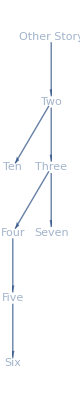

```mathematica
twineSummary[testingAssoc2]
```

### Passage Cleanup

#### Replace

```mathematica
fakePassage ="Here we are at Passage Three, try this [[link]]. Or Maybe you'd like to try [[this->Four]] or perhaps [[this->One]] or even [[that|Seven]]. Why not the [[Eight<-next]] one?";
```

```mathematica
StringReplace[fakePassage,
{
"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:>linkName,
ShortestMatch["[["~~hiddenName__~~ShortestMatch["->"~~__]~~"]]"] :> hiddenName,
ShortestMatch["[["~~hiddenName__~~ShortestMatch["|"~~__]~~"]]"] :> hiddenName,
ShortestMatch["[["~~ShortestMatch[__ ~~ "<-"]~~hiddenName__~~"]]"] :> hiddenName
}]
```

Here we are at Passage Three, try this link. Or Maybe you'd like to try this or perhaps this or even that. Why not the next one?

#### Grabbing the links correctly

```mathematica
StringReplace[fakePassage,{
"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:> Style[linkName, Red],
ShortestMatch["[["~~__~~ShortestMatch["->"~~linkName__]~~"]]"] :> Style[linkName, Orange],
ShortestMatch["[["~~__~~ShortestMatch["|"~~linkName__]~~"]]"] :> Style[linkName, Darker[Green]],
ShortestMatch["[["~~ShortestMatch[linkName__ ~~ "<-"]~~__~~"]]"] :> Style[linkName, Darker[Yellow]]
}]
```

Here we are at Passage Three, try this ~~link~~. Or Maybe you'd like to try ~~Four~~ or perhaps ~~One~~ or even ~~Seven~~. Why not the ~~Eight~~ one?

```mathematica
StringCases[fakePassage,{
"[["~~ShortestMatch[linkName___]~~"]]" /; !StringContainsQ[linkName, "->" | "<-" | "|"]:> linkName,
ShortestMatch["[["~~__~~ShortestMatch["->"~~linkName__]~~"]]"] :> linkName,
ShortestMatch["[["~~__~~ShortestMatch["|"~~linkName__]~~"]]"] :> linkName,
ShortestMatch["[["~~ShortestMatch[linkName__ ~~ "<-"]~~__~~"]]"] :> linkName
}]
```

{link,Four,One,Seven,Eight}

#### Macros

```mathematica
?Template*
```

TemplateIf[condition,tclause] represents an element of a template object that inserts tclause if the condition evaluates to True.
TemplateIf[condition,tclause,fclause] inserts fclause if the condition does not evaluate to True.

Set: <| “command” → “set”, “data” → <| “Variable” → “my-var”, “Value” → “my-val” |> |>

If: <|“command”→“if”, “data”→<|“ConditionExpression”→ (Implementation?), “Return”→ ___ |>|>

Either: <|”command”→”either”, “data”→ {x, y, z, ...}|>

```mathematica
macroGrammar2[commandAssoc_]:=Module[{command = commandAssoc["command"], data=commandAssoc["data"]},
Switch[command,
"set",ToExpression[ToString@data["Variable"]<>"="<> ToString@data["Value"]] ,
"if",If[data["ConditionExpression"], data["T"], data["E"]], (*IF*)
"print",Print[data], (*PRINT*)
"either",RandomChoice[data] (*RANDOM Choice*)
]
]
```

```mathematica
macroGrammar2[<|"command" -> "set", "data" -> <|"Variable" -> Symbol["$testVar"] , "Value" -> 10|>|>]
```

10

```mathematica
macroGrammar2[<|"command" -> "print", "data" -> "Hello World"|>]
```

Hello World

```mathematica
macroGrammar2[<|"command" -> "either", "data" ->RandomInteger[10,10]|>]
```

5

```mathematica
macroGrammar2[<|"command" -> "print", "data" ->RandomInteger[10,10]|>]
```

{10,6,8,0,7,7,0,3,4,1}

```mathematica
macroGrammar2[<|"command" -> "if", "data" -><|"ConditionExpression" -> (1 > 0), "T" -> "Is True", "E" -> "Is False"|>|>]
```

Is True

```mathematica
macroGrammar2[<|"command" -> "if", "data" -><|"ConditionExpression" -> (-1 > 0), "T" -> "Is True", "E" ->"Is False" |>|>]
```

Is False

For this macroGrammar to work I need to convert the macro in the file to an association of the form <| “command” → <command>, “data” → <data-for-command> |>